# Phase diagrams for for ladder of bosons at filling factor ν=1

### Some Settings

```mathematica
$UserBaseDirectory
```

/Users/andreas/Library/Mathematica

LinTicks::shdw: Symbol LinTicks appears in multiple contexts {CustomTicks`,Global`}; definitions in context CustomTicks` may shadow or be shadowed by other definitions.

LogTicks::shdw: Symbol LogTicks appears in multiple contexts {CustomTicks`,Global`}; definitions in context CustomTicks` may shadow or be shadowed by other definitions.

ShowTickLabels::shdw: Symbol ShowTickLabels appears in multiple contexts {CustomTicks`,Global`}; definitions in context CustomTicks` may shadow or be shadowed by other definitions.

MajorTickLength::shdw: Symbol MajorTickLength appears in multiple contexts {CustomTicks`,Global`}; definitions in context CustomTicks` may shadow or be shadowed by other definitions.

MinorTickLength::shdw: Symbol MinorTickLength appears in multiple contexts {CustomTicks`,Global`}; definitions in context CustomTicks` may shadow or be shadowed by other definitions.

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage[rgb,dvipsnames]{xcolor},\definecolor{myred}{rgb}{0.9176470588, 0.2588235294, 0.2078431373},\definecolor{myblue}{rgb}{0.2745098039, 0.5333333333, 0.9450980392},\definecolor{myyellow}{rgb}{0.9764705882, 0.7333333333, 0.1764705882},\definecolor{mygreen}{rgb}{0.2039215686, 0.662745098, 0.3176470588}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

{TripleCross,Y,UpTriangle,UpTriangleTruncated,DownTriangle,DownTriangleTruncated,LeftTriangle,LeftTriangleTruncated,RightTriangle,RightTriangleTruncated,ThreePointedStar,Cross,DiagonalCross,Diamond,Square,FourPointedStar,DiagonalFourPointedStar,FivefoldCross,Pentagon,FivePointedStar,FivePointedStarThick,SixfoldCross,Hexagon,SixPointedStar,SixPointedStarSlim,SevenfoldCross,SevenPointedStar,SevenPointedStarNeat,SevenPointedStarSlim,EightfoldCross,Disk,H,I,N,Z,S,Sw,Sl}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage[rgb,dvipsnames]{xcolor},\definecolor{myred}{rgb}{0.9176470588, 0.2588235294, 0.2078431373},\definecolor{myblue}{rgb}{0.2745098039, 0.5333333333, 0.9450980392},\definecolor{myyellow}{rgb}{0.9764705882, 0.7333333333, 0.1764705882},\definecolor{mygreen}{rgb}{0.2039215686, 0.662745098, 0.3176470588}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→10,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

SetOptions::optnf: Joined is not a known option for Plot.

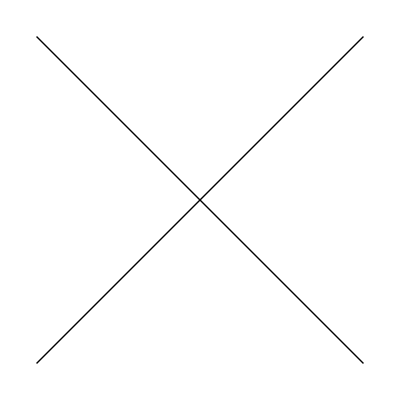
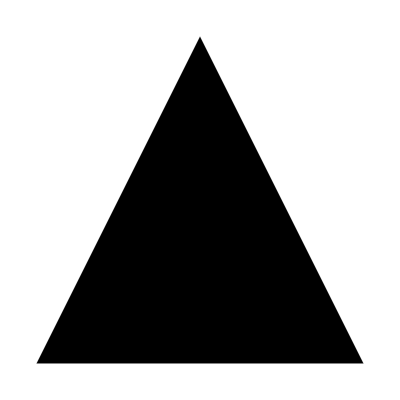
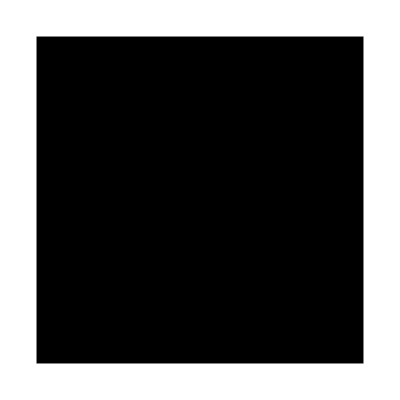
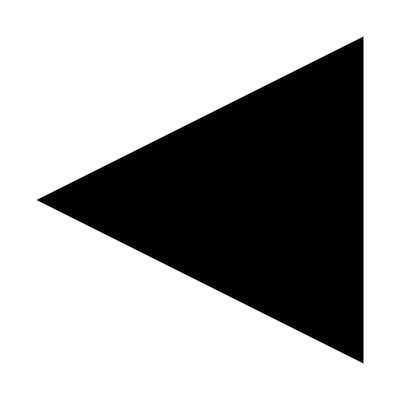
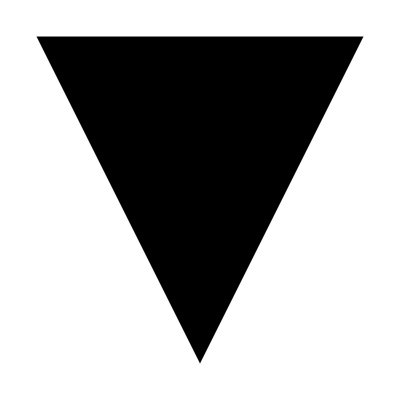
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SetDirectory[NotebookDirectory[]];
Import["CustomTicks.m"]

SetOptions[LinTicks,MajorTickLength->.02,MinorTickLength->.0125];
SetOptions[LogTicks,MajorTickLength->.02,MinorTickLength->.0125];

<<MaTeX`

SetOptions[MaTeX,"Preamble"->{"\\usepackage[rgb,dvipsnames]{xcolor}","\\definecolor{myred}{rgb}{0.9176470588, 0.2588235294, 0.2078431373}","\\definecolor{myblue}{rgb}{0.2745098039, 0.5333333333, 0.9450980392}","\\definecolor{myyellow}{rgb}{0.9764705882, 0.7333333333, 0.1764705882}","\\definecolor{mygreen}{rgb}{0.2039215686, 0.662745098, 0.3176470588}"}]

myblue=RGBColor[0.2745098039,0.5333333333,0.9450980392];
myred=RGBColor[0.9176470588,0.2588235294,0.2078431373];
mygreen=RGBColor[0.2039215686,0.662745098,0.3176470588];
myyellow=RGBColor[0.9764705882,0.7333333333,0.1764705882];
mygray=RGBColor[109/255//N,109/255//N,109/255//N];
mylightgray=RGBColor[185/255//N,185/255//N,185/255//N];
thickness=0.002;
size=0.05;
font="Latin Modern Roman";
imagSize=200;
fontSize=10;
markersize=0.025;
cm=72/2.54;
ts=0.02*{1,1/GoldenRatio};

Needs["PolygonPlotMarkers`"]

fm[name_,size_:4]:=Graphics[{EdgeForm[],PolygonMarker[name,Offset[size]]},AlignmentPoint->{0,0}];

fm2[name_,size_:3]:=Graphics[{EdgeForm[],PolygonMarker[name,Offset[size]]},AlignmentPoint->{0,0}];

allShapes=PolygonMarker[All]
Tooltip[Graphics[{FaceForm[Hue@Random[]],EdgeForm[{Black,Thickness[0.003],JoinForm["Miter"]}],PolygonMarker[#,1]},ImageSize->30,PlotRange->1.5,PlotRangePadding->0,ImagePadding->0],#]&/@allShapes

fm[name_,size_:5]:=Graphics[{EdgeForm[],PolygonMarker[name,Offset[size]]},AlignmentPoint->{0,0}];

fm2[name_,size_:3]:=Graphics[{EdgeForm[],PolygonMarker[name,Offset[size]]},AlignmentPoint->{0,0}];

GetScaledLogTicks[min_,max_,scale_]:=Module[{ticks},ticks=#[Log[min],Log[max]]&/@{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]};
(*scale the tick length*)Table[{Exp[#[[1]]],#[[2]],scale*#[[3]]}&/@ticks[[i]],{i,2}]]

SetOptions[MaTeX,FontSize->fontSize]

SetOptions[ListPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black,Directive[Black,AbsoluteThickness[0.5]]],Frame->True,Axes->False,FrameTicksStyle->Black,Joined->True,PlotMarkers->Automatic];

SetOptions[Plot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black,Directive[Black,AbsoluteThickness[0.5]]],Frame->True,Axes->False,FrameTicksStyle->Black,Joined->True,PlotMarkers->Automatic];

SetOptions[ListLogLogPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,FrameTicksStyle->Black,Joined->True,PlotMarkers->Automatic];

align = Sequence[AlignmentPoint -> {0, 0}, AxesOrigin -> {0, 0}, BaselinePosition -> Axis];
size = Sequence[PlotRange -> {{-2, 2}, {-2, 2}}, PlotRangePadding -> Scaled[edgeThickness/2 + plotRangePadding], ImagePadding -> 0, ImageMargins -> 0];
plotRangePadding = .01;
edgeThickness = .1;
size = Sequence[PlotRange -> {{-2, 2}, {-2, 2}}, PlotRangePadding -> Scaled[edgeThickness/2 + plotRangePadding], ImagePadding -> 0, ImageMargins -> 0];
halfTr = {Graphics[{EdgeForm[{mygray, AbsoluteThickness[edgeThickness], JoinForm["Round"]}], Line[{{-1, -1}, {1, 1}}], Line[{{-1, 1}, {1, -1}}](*EdgeForm[],FaceForm[Opacity[1]],Polygon[{{0,2},{2/Sqrt[3],0},{-(2/Sqrt[3]),0}}],EdgeForm[{Opacity[1],Thickness[edgeThickness],JoinForm["Round"]}],FaceForm[],Polygon[{{0,2},{Sqrt[3],-1},{-Sqrt[3],-1}}]*)}, align,PlotRangePadding->0,ImagePadding->0],
   Graphics[{EdgeForm[{mygray, AbsoluteThickness[edgeThickness], JoinForm["Round"]}], Polygon[{{0, 1}, {1, -1}, {-1, -1}}]}, align,PlotRangePadding->0,ImagePadding->0],
   Graphics[{EdgeForm[{mygray, AbsoluteThickness[edgeThickness], JoinForm["Round"]}], Rectangle[{-1, -1}, {1, 1}]}, align,PlotRangePadding->0,ImagePadding->0]};
halfTr = Flatten[{halfTr, Table[halfTr /. p : {_?NumericQ, _?NumericQ} :> RotationMatrix[θ].p, {θ, {Pi/2,  Pi}}]}, 2] /. "size" -> size
Magnify[#, .1] & /@ halfTr;
ListPlot[Flatten[Table[{{n, y}}, {y, Range[1, 3]}, {n, 20}], 1], PlotMarkers -> Table[{s, 0.07}, {s, halfTr}], PlotStyle -> ColorData[60, "ColorList"], GridLines -> {Range[20], Range[3]}, PlotRange -> {{0, 21}, {0, 4}}, Axes -> False, Frame -> True];

new={{"GoogleGradient","",{}},{"Gradients"},1,{0,1},{myblue,Lighter[myblue,.5],Lighter[myblue,.75],White,Lighter[myred,.75],Lighter[myred,.5],myred},""};
ColorData["GoogleGradient"]//Quiet;
AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];

new={{"GoogleGradientRev","",{}},{"Gradients"},1,{0,1},Reverse[{myblue,Lighter[myblue,.5],Lighter[myblue,.75],White,Lighter[myred,.75],Lighter[myred,.5],myred}],""};
ColorData["GoogleGradientRev"]//Quiet;
AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];
```

#### Colors

```mathematica
(*Luttinger liquid*)
llcol=RGBColor[{255,255,191}/256]; 
(*Color for the h term*)
hcol=RGBColor[{252,141,89}/256];
(*Color for the g term*)
gcol=RGBColor[{145,191,219}/256];
(*Color for the Luttinger parameter Subscript[K, c] of the charge sector*)
kccol=RGBColor[{228,26,28}/256];
(*Color for the Luttinger parameter Subscript[K, s] of the charge sector*)
kscol=RGBColor[{77,175,74}/256];
```

### Point plotter

```mathematica
ColoredPointPlot[datalist_]:=Module[{length,colorlistnum,colorlist,newdatalist,blist,i,theplot},
length=Length[datalist];
colorlist=Table[If[datalist[[i,3]]==0,llcol,If[datalist[[i,3]]==1,hcol,gcol]],{i,1,length}];
newdatalist=Table[{datalist[[i,1]],datalist[[i,2]]},{i,1,length}];
blist={#}&/@newdatalist;
theplot=ListPlot[blist,PlotStyle->colorlist,PlotTheme->"Scientific",AspectRatio->1];
Return[theplot];
]
```

#### Parameters of the RG equations

```mathematica
Ag=1;
Ah=1;
γ=1;
uc=4*Pi;
us=4*Pi;
```

#### Parameters of the initial conditions

```mathematica
latcon=1/Pi;
k0=Pi/2;
```

### Function Phase

```mathematica
(*The inputs of Phase function are the interaction energies of the initial tight binding model (over the intrachain hopping energy): {Subscript[u, up,up],Subscript[u, up,down],Subscript[v, up,up],Subscript[v, up,down],Ω}. The output of Phase function is the following list: {{solution of the RG equations (before evaluation)},{phase indicator(where 0=Luttinger liquid;1=h-dominated phase,2=g-dominated phase),the gap,hStop,gStop,KcStop,KsStop,lStop,Plot of the evolution for h and g,Plot of the evolution for Subscript[K, c] and Subscript[K, s]}}*)
Phase[u1_,u2_,v1_,v2_,w0_]:=Module[{Kc0,Ks0,h0,g0,lowcut,upcut,s,lStop,gStop,hStop,KcStop,KsStop,phase,gap},
(*INITIAL CONDITIONS*)
Kc0=Sqrt[latcon*Pi/(u1+u2+2*v1+2*v2)];
Ks0=Sqrt[latcon*Pi/(u1-u2+2*v1-2*v2)];
h0=(2*Cos[2*k0*latcon]*v2+u2)/(2*latcon^2*Pi^2);
g0=w0/(2*latcon*Pi);
(*LOWER energy cut-off*)
lowcut=0.01;
(*UPPER energy cut-off*)
upcut=1;
(*THE SOLVER (Use a Runge Kutta specifier if possible, it is optimal for Mathematica 10.4)*)
s=NDSolve[{
h'[l]==Expand[h[l]*(2-2*Ks[l])+g[l]^2*γ*(Kc[l]-Ks[l]+1/Ks[l])],
g'[l]==Expand[g[l]*(2-(Kc[l]+Ks[l]+1/Ks[l])/2)-h[l]*g[l]*γ*Ks[l]],
Kc'[l]==Expand[g[l]^2*4*Pi*Ag/uc^2*2*(Kc[l]+Ks[l]+1/Ks[l])/2]*Kc[l]^2,
Ks'[l]==Expand[-4*Pi/us^2*(h[l]^2*2*Ah*Ks[l]^3+g[l]^2*Ag*2*(Kc[l]+Ks[l]+1/Ks[l])/2*(1-Ks[l]^2))],
h[0]==h0,g[0]==g0,Kc[0]==Kc0,Ks[0]==Ks0,WhenEvent[(g[l]>upcut||h[l]>upcut||(g[l]<lowcut&&h[l]<lowcut)),{lStop=l,"StopIntegration"}]},
{h,g,Kc,Ks},{l,0,∞}];
(*Values of all variables in the last step*)
hStop=Evaluate[h[lStop]/.s];
gStop=Evaluate[g[lStop]/.s];
KcStop=Evaluate[Kc[lStop]/.s];
KsStop=Evaluate[Ks[lStop]/.s];
(*PHASE, 0 corresponds to Luttinger liquid, 1 to the h-dominated phase, 2 to the g-dominated phase,*)
If[hStop[[1]]>=upcut-lowcut,phase=1; gap=Exp[-lStop];,
If[gStop[[1]]>=upcut-lowcut,phase=2;gap=Exp[-lStop];,
phase=0;gap=0;];];
(*RETURN*)
Return[
{s,Flatten[{phase,gap,hStop,gStop,KcStop,KsStop,lStop,
Plot[Evaluate[{g[l],h[l]}/.s],{l,0,lStop},PlotRange->All,FrameLabel->"l",PlotTheme->"Scientific", PlotStyle->{gcol,hcol},PlotLegends->{"g","h"}],
Plot[Evaluate[{Kc[l],Ks[l]}/.s],{l,0,lStop},PlotRange->All,FrameLabel->"l",FrameLabel->None,PlotTheme->"Scientific",PlotStyle->{kccol,kscol},PlotLegends->{"K_c","K_s"}]}]}];
]
```

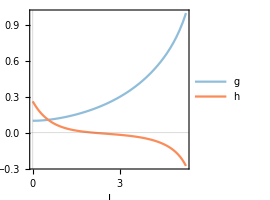
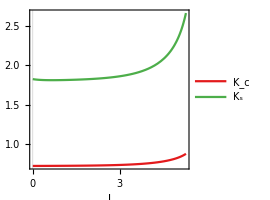
{{{h→InterpolatingFunction[…],g→InterpolatingFunction[…],Kc→InterpolatingFunction[…],Ks→InterpolatingFunction[…]}},{2,0.00501874,-0.277836,1.,0.879252,2.66281,5.29458,-Graphics-,-Graphics-}}

```mathematica
(*Try Phase here*)
Phase[0.3,0.2,0.4,0.3,0.2]
```

### Animator for different initial conditions

```mathematica
phasesanimever=Table[Phase[1,u2p,0,0,0.1],{u2p,0.03,0.99,0.05}];
phasesanimehor=Table[Phase[u1p,0.1,0,0,0.1],{u1p,0.1,2,0.02}];
ListAnimate[Table[{phasesanimever[[a]][[2]][[8]],phasesanimever[[a]][[2]][[9]]},{a,1,Length[phasesanimever]}]]
ListAnimate[Table[{phasesanimehor[[a]][[2]][[8]],phasesanimehor[[a]][[2]][[9]]},{a,1,Length[phasesanimehor]}]]
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between l = 49.5906 and l = 49.744.

Power::infy: Infinite expression 1/0. encountered.

Solve::infc: The system Ks==ComplexInfinity contains an infinite object ComplexInfinity.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between l = 43.8662 and l = 44.0376.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between l = 41.2147 and l = 41.7734.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between l = 61.5509 and l = 62.6731.

General::stop: Further output of NDSolve::evcvmit will be suppressed during this calculation.

### Function PhaseDiagramUV

```mathematica
(*The inputs of PhaseDiagramUV function are the number of different, random initial conditions for which the RG equations are to be numericaly solved and the initial intrachain hopping energy (over the intrachain hopping energy): {n,Ω}.*)
PhaseDiagramUV[n_,w0_]:=Module[{i,u1,u2,v1,v2,phaselist,gaplist,Kc0,Ks0,h0,g0,lowcut,upcut,s,lStop,gStop,hStop,KcStop,KsStop,phase,gap,phasediag,gapdiag},
phaselist={};
gaplist={};
(*INITIAL INTERACTION ENERGIES SAMPLER*)
For[i=0,i<n,i++,
u1=RandomReal[{0,0.5}];
v1=RandomReal[{0,u1}];
u2=RandomReal[{0,u1}];
v2=RandomReal[{0,v1}];
(*INITIAL CONDITIONS*)
Kc0=Sqrt[latcon*Pi/(u1+u2+2*v1+2*v2)];
Ks0=Sqrt[latcon*Pi/(u1-u2+2*v1-2*v2)];
h0=(2*Cos[2*k0*latcon]*v2+u2)/(2*latcon^2*Pi^2);
g0=w0/(2*latcon*Pi);
(*LOWER energy cut-off*)
lowcut=0.01;
(*UPPER energy cut-off*)
upcut=1;
(*THE SOLVER (Use a Runge Kutta specifier if possible, it is optimal for Mathematica 10.4)*)
s=NDSolve[{
h'[l]==Expand[h[l]*(2-2*Ks[l])+g[l]^2*γ*(Kc[l]-Ks[l]+1/Ks[l])],
g'[l]==Expand[g[l]*(2-(Kc[l]+Ks[l]+1/Ks[l])/2)-h[l]*g[l]*γ*Ks[l]],
Kc'[l]==Expand[g[l]^2*4*Pi*Ag/uc^2*2*(Kc[l]+Ks[l]+1/Ks[l])/2]*Kc[l]^2,
Ks'[l]==Expand[-4*Pi/us^2*(h[l]^2*2*Ah*Ks[l]^3+g[l]^2*Ag*2*(Kc[l]+Ks[l]+1/Ks[l])/2*(1-Ks[l]^2))],
h[0]==h0,g[0]==g0,Kc[0]==Kc0,Ks[0]==Ks0,WhenEvent[(g[l]>upcut||h[l]>upcut||(g[l]<lowcut&&h[l]<lowcut)),{lStop=l,"StopIntegration"}]},
{h,g,Kc,Ks},{l,0,∞}];
(*Values of all variables in the last step*)
hStop=Evaluate[h[lStop]/.s];
gStop=Evaluate[g[lStop]/.s];
KcStop=Evaluate[Kc[lStop]/.s];
KsStop=Evaluate[Ks[lStop]/.s];
(*PHASE, 0 corresponds to Luttinger liquid, 1 to the h-dominated phase, 2 to the g-dominated phase,*)
If[hStop[[1]]>=upcut-lowcut,phase=1; gap=Exp[-lStop];,
If[gStop[[1]]>=upcut-lowcut,phase=2;gap=Exp[-lStop];,
phase=0;gap=0;];];
(*Next, the result for the specific initial conditions is registered in phaselist and gaplist*)
AppendTo[phaselist,{u1+2*v1,u2+2*v2,phase}];
AppendTo[gaplist,{u1+2*v1,u2+2*v2,gap}];
];
phasediag=Show[ColoredPointPlot[phaselist],FrameLabel->{"U_(↑↑)+ 2V_(↑↑)","U_(↑↓)+ 2V_(↑↓)"}];gapdiag=ListContourPlot[gaplist,PlotLegends->Automatic,InterpolationOrder->1,ContourStyle->{Thick},ContourLabels->True,Contours->3,ContourShading->None,FrameLabel->{"U_(↑↑)+ 2V_(↑↑)","U_(↑↓)+ 2V_(↑↓)"},BaseStyle->{FontWeight->"Bold",FontSize->14}];
(*RETURN*)
Return[Show[phasediag,gapdiag]];
]
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between l = 41.7736 and l = 42.1441.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between l = 53.9872 and l = 54.2838.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between l = 40.9324 and l = 41.3106.

General::stop: Further output of NDSolve::evcvmit will be suppressed during this calculation.

NDSolve::ndsz: At l == 8.61004, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At l == 9.18928, step size is effectively zero; singularity or stiff system suspected.

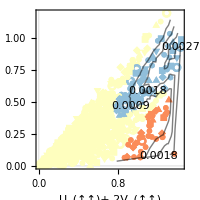

```mathematica
(*Try PhaseDiagramUV here*)
PhaseDiagramUV[1000,0.1]
```

### 1st order result for K_s and K_c

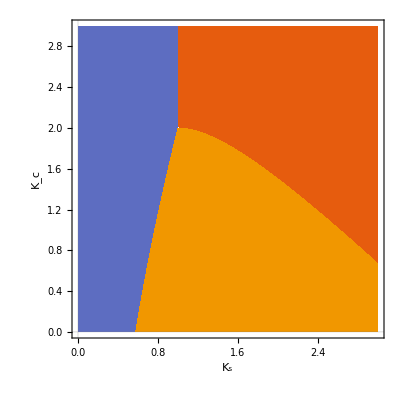

```mathematica
Dg=(Kc+Ks+1/Ks)/2;
Dh=2*Ks;
PhaseDiagramK1=RegionPlot[{Dg>2&&Dh>2,Dh<2&&Dg>Dh,Dg<2&&Dg<Dh},{Ks,0,3},{Kc,0,3},PlotStyle->{llcol,hcol,gcol},FrameLabel->{"K_s","K_c"},PlotTheme->"Scientific",BoundaryStyle->None]
```

### Function PhaseDiagramK (2nd order result for K_s and K_c)

```mathematica
Ag=1;
Ah=1;
γ=1;
uc=4*Pi;
us=4*Pi;
(*The inputs of PhaseDiagramK function are the number of different, random initial conditions for which the RG equations are to be numericaly solved and the initial intrachain hopping energy (over the intrachain hopping energy): {n,Ω}.*)
Clear[PhaseDiagramK2]
PhaseDiagramK2[nx_,ny_,g0_]:=Module[{h0,i,j,kflow,phaselist,phaselist2,Kc0,Ks0,lowcut,upcut,s,lStop,gStop,vperp,hStop,KcStop,KsStop,phase,phasediag},
kflow={};
phaselist={};
phaselist2={};
(*INITIAL INTERACTION ENERGIES SAMPLER*)
Monitor[
For[i=0,i≤nx,i++,
For[j=1,j≤ny,j++,
(*INITIAL CONDITIONS*)
Kc0=i/nx*2.5;
Ks0=j/ny*3;

h0=8g0; (* the easiest approximation *)
h0=(Kc0^2-Ks0^2)/(8π); (* we assume vF to be 0.5, and this is only valid for small interactions... *)
(*In the thesis we had fixed cos(2*latcon*k0) to 1/2, so I used the initial condition h0=(-Kc0^2+Ks0^2)/(4 Kc0^2 Ks0^2 π^2). I think that was a mistake, h0 should be independent than Ks0 and Kc0(?)*)
(*LOWER energy cut-off*)
lowcut=0.001;
(*UPPER energy cut-off*)
upcut=1;

(*THE SOLVER (Use a Runge Kutta specifier if possible, it is optimal for Mathematica 10.4)*)
s=NDSolve[{
h'[l]==Expand[h[l]*(2-2*Ks[l])+g[l]^2*γ*(Kc[l]-Ks[l]+1/Ks[l])],
g'[l]==Expand[g[l]*(2-(Kc[l]+Ks[l]+1/Ks[l])/2)-h[l]*g[l]*γ*Ks[l]],
Kc'[l]==Expand[g[l]^2*4*Pi*Ag/uc^2*2*(Kc[l]+Ks[l]+1/Ks[l])/2]*Kc[l]^2,
Ks'[l]==Expand[-4*Pi/us^2*(h[l]^2*2*Ah*Ks[l]^3+g[l]^2*Ag*2*(Kc[l]+Ks[l]+1/Ks[l])/2*(1-Ks[l]^2))],
h[0]==h0,g[0]==g0,Kc[0]==Kc0,Ks[0]==Ks0,WhenEvent[Abs[g[l]]>upcut||Abs[h[l]]>upcut||(Abs[g[l]]<lowcut&&Abs[h[l]]<lowcut),{lStop=l,"StopIntegration"}]},
{h,g,Kc,Ks},{l,0,∞}];
(*Values of all variables in the last step*)
hStop=Evaluate[h[lStop]/.s];
gStop=Evaluate[g[lStop]/.s];
KcStop=Evaluate[Kc[lStop]/.s];
KsStop=Evaluate[Ks[lStop]/.s];
(*PHASE, 0 corresponds to Luttinger liquid, 1 to the h-dominated phase, 2 to the g-dominated phase,*)
phase=0;
If[(Abs[hStop[[1]]]>Abs[gStop[[1]]]>lowcut),phase=1;];
If[(Abs[gStop[[1]]]>Abs[hStop[[1]]]>lowcut),phase=2;];
(*Next, the result for the specific initial conditions is registered in phaselist*)
AppendTo[phaselist,{Kc0,Ks0,phase}];
AppendTo[phaselist2,Flatten[{KcStop,KsStop,phase}]];
AppendTo[kflow,Flatten[{h0,KcStop,KsStop}]];
];
];
,{i,j}];
(*phasediag=Show[ColoredPointPlot[phaselist],FrameLabel->{"K_s","K_c"}];*)
(*RETURN*)
Return[{phasediag,phaselist,phaselist2,kflow}];
]
```

```mathematica
list=Get["rgdata.wl"];
```

```mathematica
(*Try PhaseDiagramK2 here*)
nn=32;
{plot,list1,list2,list3}=PhaseDiagramK2[nn,nn,0.1/(2π)]//Quiet;
```

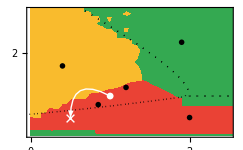

```mathematica
rgplot=Show[ListPlot[{{}}],ListContourPlot[list2,InterpolationOrder->0,Contours->2,ContourShading->{mygreen,myred,myyellow},ContourStyle->None],RegionPlot[{Dg>2&&Dh>2,Dh<2&&Dg>Dh,Dg<2&&Dg<Dh},{Kc,-1,5},{Ks,-1,8},PlotStyle->Transparent,FrameLabel->MaTeX[{"K_c","K_s"}],BoundaryStyle->Directive[Black,Dotted,AbsoluteThickness[1]]],Graphics[{White,Arrow[BezierCurve[{{1,1},{0.5,1.5},{0.5,0.5}}]]}],PlotRange->{{0.,2.5},{0.1,3}},FrameLabel->MaTeX[{"K_c","K_s"}],PlotRangePadding->0,AspectRatio->1/GoldenRatio,ImageSize->8.6cm,Epilog->{Inset[Graphics[{{White,Line[{{-1,-1},{1,1}}]},{White,Line[{{-1,1},{1,-1}}]}},ImageSize->8],{0.5,0.5}],Inset[Graphics[{White,Disk[]},ImageSize->7],{1,1}],Inset[MaTeX["\\color{white}h\\text{-phase}"],{2,0.5}],Inset[MaTeX["\\color{white}{\\rm Luttinger\\ liquid}"],{1.9,2.25}],Inset[MaTeX["\\color{white}g\\text{-phase}"],{0.4,1.7}],Inset[MaTeX["\\color{white}\\text{HCB}"],{1.2,1.2}],Inset[MaTeX["\\color{white}V_\\perp>0"],{0.85,0.8}]},FrameTicks-> {{LinTicks[0,4,1,5],LinTicks[0,4,1,5,ShowTickLabels->False]},{LinTicks[0,4,1,5],LinTicks[0,4,1,5,ShowTickLabels->False]}},ImagePadding->{{30,5},{40,5}}]
```

```mathematica
Show[ListPlot[{{}},PlotRange->{{0,2.5},{3/nn,3}}],ListDensityPlot[{list1[[All,1]],list1[[All,2]],list2[[All,1]]}ᵀ,InterpolationOrder->0],FrameLabel->MaTeX[{"K_c(0)","K_s(0)"}],ImageSize->8.6cm/2,AspectRatio->1,PlotLabel->MaTeX["K_c(l)"]]
Show[ListPlot[{{}},PlotRange->{{0,2.5},{3/nn,3}}],ListDensityPlot[{list1[[All,1]],list1[[All,2]],list2[[All,2]]}ᵀ,InterpolationOrder->0],FrameLabel->MaTeX[{"K_c(0)","K_s(0)"}],ImageSize->8.6cm/2,AspectRatio->1,PlotLabel->MaTeX["K_s(l)"]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/andreas/Dropbox/Bosonic ladders/notes of Apollo's work

```mathematica
Export["RG.png",rgplot,ImageResolution->1200]
```

RG.png